Apparently, the phase of the third harmonic module is not that important, except it should be around 180 deg. Changing by +- 10 degrees doesn’t seem to make a difference as far as linearity of the phase space is concerned.
It does affect the chirp though.

```mathematica
SetOptions[Manipulator,Appearance->"Open"];
```

```mathematica
f=1.3 10^9;
c=3 10^8;
T=1/f;
λ=c T;
k=2π/λ;
VACC1=150;
```

```mathematica
W[z_,V_, ϕ_,k_ ]:=V Cos[k z + Degree ϕ]
WACC1[z_,ϕ_]:=W[z, VACC1, ϕ, k]
WACC39[z_,ϕ_,ratio_]:=W[z, VACC1/ratio, ϕ, 3k]
Wtot[z_,ϕACC1_,ϕACC39_,ratio_]:=WACC1[z, ϕACC1]+WACC39[z, ϕACC39,ratio]
```

```mathematica
Manipulate[
Plot[ 
{Wtot[z,ϕACC1,ϕACC39,ratio], WACC1[z,ϕACC1],WACC39[z,ϕACC39,ratio]
         (*Evaluate[D[D[Wtot[z,ϕACC1,ϕACC39],z],z]],*)
},
          {z,-0.1,0.1},
PlotRange->{-170,170},
PlotLegends-> {"Total", "ACC1", "ACC39"}
],
{{ϕACC1,0},-180,180},
   { {ϕACC39,180},-180,180},
{ {ratio,9},1,20}
]
```

Define and plot particle distribution after the gun

```mathematica
Nparticles=1000;
σzGun=1*10^-3; (*1mm*)
EGun=5; (*MeV*)
R56=0.18;
Nbins=30;
zGun=RandomVariate[NormalDistribution[0,σzGun],Nparticles];
δGun=RandomVariate[UniformDistribution[{0,0}],Nparticles];
```

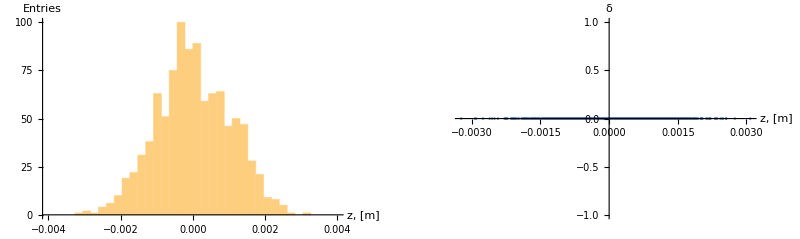

```mathematica
zGunPlot=Histogram[zGun,{"Raw",Nbins},PlotRange->{{-4*σzGun,4*σzGun},{0,Nparticles/10}},AxesLabel->{"z, [m]","Entries"}];
zδGunPlot=ListPlot[Table[{zGun[[n]],δGun[[n]]},{n,Nparticles}],AxesLabel->{"z, [m]","δ"}];
GraphicsRow[{zGunPlot,zδGunPlot}]
```

Track through ACC1,  ACC39 and BC2

```mathematica
Manipulate[
(* track through ACC1 and ACC39 *)
δACC39=ConstantArray[0,Nparticles];
EACC39=EGun+Wtot[0,ϕACC1,ϕACC39,ratio];
Do[δACC39[[n]]=((1+δGun[[n]])*EGun+Wtot[zGun[[n]],ϕACC1,ϕACC39,ratio]-EACC39)/EACC39,{n,Nparticles}];
zACC39=zGun;
(* plot *)
zACC39Plot=Histogram[zACC39,Nbins,AxesLabel->{"z, [m]","Entries"},PlotRange->{{-4*σzGun,4*σzGun},{0,Nparticles/10}},PlotLabel->"after ACC39"];
zδACC39Plot=ListPlot[Table[{zACC39[[n]],δACC39[[n]]},{n,Nparticles}],AxesLabel->{"z, [m]","δ"},PlotRange->{{-3*σzGun,3*σzGun},{-0.05,0.05}},PlotLabel->"after ACC39"];
(* track through BC2 *)
δBC2=δACC39;
zBC2=ConstantArray[0,Nparticles];
Do[zBC2[[n]]=zACC39[[n]]+R56*δACC39[[n]],{n,Nparticles}];
(* plot *)
zBC2Plot=Histogram[zBC2,{"Raw",Nbins},AxesLabel->{"z, [m]","Entries"},PlotRange->{{-4*σzGun,4*σzGun},{0,Nparticles/10}},PlotLabel->"after BC2"];
zBC2PlotNoZoom=Histogram[zBC2,{"Raw",Nbins},AxesLabel->{"z, [m]","Entries"},PlotLabel->"after BC2"];
zδBC2Plot=ListPlot[Table[{zBC2[[n]],δBC2[[n]]},{n,Nparticles}],AxesLabel->{"z, [m]","δ"},PlotRange->{{-3*σzGun,3*σzGun},{-0.05,0.05}},PlotLabel->"after BC2"];
GraphicsGrid[{{zACC39Plot,zδACC39Plot},{zBC2Plot,zδBC2Plot},{zBC2PlotNoZoom}}],
{{ϕACC1,0},-10,10},{{ϕACC39,180},160,180},{{ratio,9},1,15},{ratio,{10000}}
]
```

```mathematica
(*triagnular 'driver'*)
(*4, 165.5, 7.18*)
(*4, 163.86, 6.46*)
(*triagnular 'witness'*)
(*10, 180, 14.58*)
```